Закон движения мяча без сопротвления воздуза

Ox: 2.02456 t

Oy: -4.9 (-0.367347-1.78966 t+1. t^2)

Момент касания земли

t = 1.9756

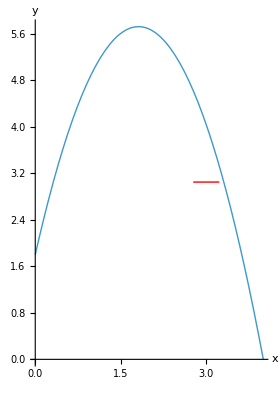

время tk

1.63349

Координата центра мяча в момент tk

3.3071

точность броска

-3.07096×10^-1м

Коридор попадания

0.103895

Не попадание

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Закон движения мяча с сопротивлением воздуха

Ox: 29.5072 ⅇ^(-0.0686124 t) (-1.+1. ⅇ^(0.0686124 t))

Oy: -142.831 ⅇ^(-0.0686124 t) (15.4695-15.4821 ⅇ^(0.0686124 t)+1. ⅇ^(0.0686124 t) t)

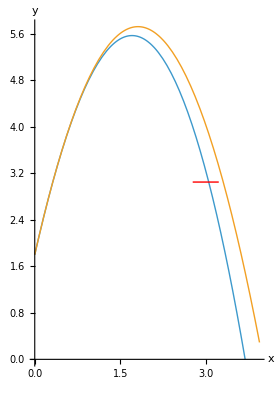

Время tk

1.5915-3.39813×10^-15 ⅈ

Координата центра мяча в момент tk

3.0524-6.16804×10^-15 ⅈ

точность броска

-5.23973×10^-2+(6.16804×10^-15) ⅈм

Коридор попадания

0.104433

Попадание

Вектор уголовой скорости: {0,0,0.5}

-Graphics3D-

Вектор уголовой скорости: {0,0.5,0}

-Graphics3D-

Вектор уголовой скорости: {0,-0.08,0}

-Graphics3D-

```mathematica
ClearAll["Global`*"]



(*Параметры системы*)
m=0.6;
R=0.12;
rk=0.457/2;
hk=3.05;
L=3;
x0=0;
y0=1.8;
v0=9;
a0=77;
μ=0.0182;
kr=6 π μ R;
g=9.8;
ω=0.5;


(* ====Движение мяча без учета силы сопротивления.Аналитическое решение=============*)
dEqx0={m x''[t]==0};
dEqy0={m y''[t]+m g==0};
InCondx={x[0]==x0,x'[0]==Cos[a0 Degree] v0};
InCondy={y[0]==y0,y'[0]==Sin[a0 Degree] v0};
SolDEqx0=DSolve[Join[dEqx0,InCondx],x[t],t][[1,1,2]];
SolDEqy0=DSolve[Join[dEqy0,InCondy],y[t],t][[1,1,2]];
Print[Style["Закон движения мяча без сопротвления воздуза",18]];
Print[Style["Ox: ",14],SolDEqx0]
Print[Style["Oy: ",14],SolDEqy0]

Print[Style["Момент касания земли",18]];
tk=Max[Solve[SolDEqy0==0,t][[1,1,2]],Solve[SolDEqy0==0,t][[2,1,2]]];
Print[Style["t = "],tk]


Gr1=ParametricPlot[{SolDEqx0,SolDEqy0},{t,0,tk},AxesLabel->{Style[x,16],Style[y,16]},PlotStyle->Thick];
Gr2=Graphics[{Thick,Red,Line[{{L-rk,hk},{L+rk,hk}}]}];
Show[Gr1,Gr2]

(* ==================Оценка точности броска без сопротивления воздуха=============*)Print["время tk"]
 NSolve[SolDEqy0==hk,t][[2,1,2]]
 Print[Style["Координата центра мяча в момент tk",18]]
 xtk0=SolDEqx0/. t->NSolve[SolDEqy0==hk,t][[2,1,2]] 
Print[Style["точность броска",18]] 
Print[ScientificForm[L-xtk0],"м"] 
vxtk=D[SolDEqx0,t]/. t->NSolve[SolDEqy0==hk,t][[2,1,2]];
vytk=D[SolDEqy0,t]/. t->NSolve[SolDEqy0==hk,t][[2,1,2]];
ϕ=ArcTan[Abs[vytk/vxtk]];
Print[Style["Коридор попадания",18]]
 d=rk-R/Sin[ϕ]
 If[Abs[L-xtk0]<=d,Print[Style["Попадание",18,Red]],Print[Style["Не попадание",14,Blue]]]

(* =======Движение мяча с учетом силы сопротивления.Аналитическое решение===============*)

dEqx1={m x''[t]+kr x'[t]==0};
dEqy1={m y''[t]+kr y'[t]+m g==0};
InCondx={x[0]==x0,x'[0]==Cos[a0 Degree] v0};
InCondy={y[0]==y0,y'[0]==Sin[a0 Degree] v0};
SolDEqx1=DSolve[Join[dEqx1,InCondx],x[t],t][[1,1,2]];
SolDEqy1=DSolve[Join[dEqy1,InCondy],y[t],t][[1,1,2]];
tk=Max[Solve[SolDEqy1==0,t][[1,1,2]],Solve[SolDEqy1==0,t][[2,1,2]]];

Print[Style["Закон движения мяча с сопротивлением воздуха",18]];

Print[Style["Ox: ",14],SolDEqx1]
Print[Style["Oy: ",14],SolDEqy1]

Gr3=ParametricPlot[{{SolDEqx1,SolDEqy1},{SolDEqx0,SolDEqy0}},{t,0,tk},AxesLabel->{Style[x,16],Style[y,16]},PlotStyle->Thick];
Show[Gr3,Gr2]

(* ================= Оценка точности броска с сопротивлением воздуха==============*)
Print[Style["Время tk",18]] 
NSolve[SolDEqy1==hk,t][[2,1,2]] (*время tx*) 
Print[Style["Координата центра мяча в момент tk",18]] 
xtk1=SolDEqx1/. t->NSolve[SolDEqy1==hk,t][[2,1,2]](*координата центра мяча в момент tx*)
 Print[Style["точность броска",18]] 
Print[ScientificForm[L-xtk1],"м"] 
vxtk=D[SolDEqx1,t]/. t->NSolve[SolDEqy1==hk,t][[2,1,2]];
vytk=D[SolDEqy1,t]/. t->NSolve[SolDEqy1==hk,t][[2,1,2]];
ϕ=ArcTan[Abs[vytk/vxtk]];
Print[Style["Коридор попадания",18]]
 d=rk-R/Sin[ϕ] 
If[Abs[L-xtk1]<=d,Print[Style["Попадание",18,Red]],Print[Style["Не попадание",14,Blue]]](* ====Движение мяча с учетом силы сопротивления воздуха и силы Магнуса 3D.Решение методом Эйлера=====*)

Clear[NN,xx0,xx1,yy0,yy1,vx0,vx1,vy0,vy1];

NN=200;

xyzList=Table[0,{i,1,NN},{j,1,3}]; (*координаты мяча с силой Магнуса*)
xyz0List=Table[0,{i,1,NN},{j,1,3}]; (*координаты мяча без силы Магнуса*)

ωω={0,0,0.5}; (*вектор угловой скорости мяча*)
Print[Style["Вектор уголовой скорости: ",18],ωω]

xx0=x0; (*начальные координаты мяча с учетом эффекта и без него*)
xx1=x0;
yy0=0;
yy1=0;
zz0=y0;
zz1=y0;

vx0=Cos[a0 Degree] v0;
(*начальные скорости мяча с учетом эффекта и без него*)
vx1=Cos[a0 Degree] v0;
vy0=0;
vy1=0;
vz0=Sin[a0 Degree] v0;
vz1=Sin[a0 Degree] v0;

dt=0.01;
eps=0.1;
t=0;
i=1;

While[(zz0>eps&&zz1>eps)&&i<=NN,(*вычисления без учета эффекта Магнуса*)vx0=vx0+dt (-kr/m vx0);
vy0=vy0+dt (-kr/m vy0);
vz0=vz0+dt (-kr/m vz0-g);
xx0=xx0+dt vx0;
yy0=yy0+dt vy0;
zz0=zz0+dt vz0;
xyz0List[[i,1]]=xx0;
xyz0List[[i,2]]=yy0;
xyz0List[[i,3]]=zz0;
(*вычисления с учетом эффекта Магнуса*)vx1=vx1+dt (-kr/m vx1+2 (ωω[[2]] vz1-ωω[[3]] vy1));
vy1=vy1+dt (-kr/m vy1+2 (ωω[[3]] vx1-ωω[[1]] vz1));
vz1=vz1+dt (-kr/m vz1-g+2 (ωω[[1]] vy1-ωω[[2]] vx1));
xx1=xx1+dt vx1;
yy1=yy1+dt vy1;
zz1=zz1+dt vz1;
xyzList[[i,1]]=xx1;
xyzList[[i,2]]=yy1;
xyzList[[i,3]]=zz1;
t=t+dt;
i=i+1;];

(*Удаляем нулевые элементы*)
xyz0ListClean=Take[xyz0List,i-1];
xyzListClean=Take[xyzList,i-1];

GrMx=ListPointPlot3D[{xyz0ListClean,xyzListClean},BoxRatios->Automatic,AxesLabel->{Style[x,18],Style[y,18],Style[z,18]},PlotLabel->Style["Траектория мяча",16],PlotLegends->PointLegend[{Directive[Blue,AbsolutePointSize[6]],Directive[Orange,AbsolutePointSize[6]]},{"Без эффекта Магнуса","С эффектом Магнуса"}]];
Grωω=Graphics3D[Arrow[{{0,0,0},ωω}]];
Show[GrMx,Grωω]


Clear[NN,xx0,xx1,yy0,yy1,vx0,vx1,vy0,vy1,xyz0List,xyzList,xyz0ListClean,xyzListClean,ωω];

NN=200;

xyzList=Table[0,{i,1,NN},{j,1,3}]; (*координаты мяча с силой Магнуса*)
xyz0List=Table[0,{i,1,NN},{j,1,3}]; (*координаты мяча без силы Магнуса*)

ωω={0,0.5,0}; (*вектор угловой скорости мяча*)
Print[Style["Вектор уголовой скорости: ",18],ωω]

xx0=x0; (*начальные координаты мяча с учетом эффекта и без него*)
xx1=x0;
yy0=0;
yy1=0;
zz0=y0;
zz1=y0;

vx0=Cos[a0 Degree] v0;
(*начальные скорости мяча с учетом эффекта и без него*)
vx1=Cos[a0 Degree] v0;
vy0=0;
vy1=0;
vz0=Sin[a0 Degree] v0;
vz1=Sin[a0 Degree] v0;

dt=0.01;
eps=0.1;
t=0;
i=1;

While[(zz0>eps&&zz1>eps)&&i<=NN,(*вычисления без учета эффекта Магнуса*)vx0=vx0+dt (-kr/m vx0);
vy0=vy0+dt (-kr/m vy0);
vz0=vz0+dt (-kr/m vz0-g);
xx0=xx0+dt vx0;
yy0=yy0+dt vy0;
zz0=zz0+dt vz0;
xyz0List[[i,1]]=xx0;
xyz0List[[i,2]]=yy0;
xyz0List[[i,3]]=zz0;
(*вычисления с учетом эффекта Магнуса*)vx1=vx1+dt (-kr/m vx1+2 (ωω[[2]] vz1-ωω[[3]] vy1));
vy1=vy1+dt (-kr/m vy1+2 (ωω[[3]] vx1-ωω[[1]] vz1));
vz1=vz1+dt (-kr/m vz1-g+2 (ωω[[1]] vy1-ωω[[2]] vx1));
xx1=xx1+dt vx1;
yy1=yy1+dt vy1;
zz1=zz1+dt vz1;
xyzList[[i,1]]=xx1;
xyzList[[i,2]]=yy1;
xyzList[[i,3]]=zz1;
t=t+dt;
i=i+1;];

(*Удаляем нулевые элементы*)
xyz0ListClean=Take[xyz0List,i-1];
xyzListClean=Take[xyzList,i-1];

GrMy=ListPointPlot3D[{xyz0ListClean,xyzListClean},BoxRatios->Automatic,AxesLabel->{Style[x,18],Style[y,18],Style[z,18]},PlotLabel->Style["Траектория мяча",16],PlotLegends->PointLegend[{Directive[Blue,AbsolutePointSize[6]],Directive[Orange,AbsolutePointSize[6]]},{"Без эффекта Магнуса","С эффектом Магнуса"}]];
Grωω=Graphics3D[Arrow[{{0,0,0},ωω}]];
Show[GrMy,Grωω]

Clear[NN,xx0,xx1,yy0,yy1,vx0,vx1,vy0,vy1,xyz0List,xyzList,xyz0ListClean,xyzListClean,ωω];

NN=200;

xyzList=Table[0,{i,1,NN},{j,1,3}]; (*координаты мяча с силой Магнуса*)
xyz0List=Table[0,{i,1,NN},{j,1,3}]; (*координаты мяча без силы Магнуса*)

ωω={0,-0.08,0}; (*вектор угловой скорости мяча*)
Print[Style["Вектор уголовой скорости: ",18],ωω]


xx0=x0; (*начальные координаты мяча с учетом эффекта и без него*)
xx1=x0;
yy0=0;
yy1=0;
zz0=y0;
zz1=y0;

vx0=Cos[a0 Degree] v0;
(*начальные скорости мяча с учетом эффекта и без него*)
vx1=Cos[a0 Degree] v0;
vy0=0;
vy1=0;
vz0=Sin[a0 Degree] v0;
vz1=Sin[a0 Degree] v0;

dt=0.01;
eps=0.1;
t=0;
i=1;

While[(zz0>eps&&zz1>eps)&&i<=NN,(*вычисления без учета эффекта Магнуса*)vx0=vx0+dt (-kr/m vx0);
vy0=vy0+dt (-kr/m vy0);
vz0=vz0+dt (-kr/m vz0-g);
xx0=xx0+dt vx0;
yy0=yy0+dt vy0;
zz0=zz0+dt vz0;
xyz0List[[i,1]]=xx0;
xyz0List[[i,2]]=yy0;
xyz0List[[i,3]]=zz0;
(*вычисления с учетом эффекта Магнуса*)vx1=vx1+dt (-kr/m vx1+2 (ωω[[2]] vz1-ωω[[3]] vy1));
vy1=vy1+dt (-kr/m vy1+2 (ωω[[3]] vx1-ωω[[1]] vz1));
vz1=vz1+dt (-kr/m vz1-g+2 (ωω[[1]] vy1-ωω[[2]] vx1));
xx1=xx1+dt vx1;
yy1=yy1+dt vy1;
zz1=zz1+dt vz1;
xyzList[[i,1]]=xx1;
xyzList[[i,2]]=yy1;
xyzList[[i,3]]=zz1;
t=t+dt;
i=i+1;];

(*Удаляем нулевые элементы*)
xyz0ListClean=Take[xyz0List,i-1];
xyzListClean=Take[xyzList,i-1];

GrMz=ListPointPlot3D[{xyz0ListClean,xyzListClean},BoxRatios->Automatic,AxesLabel->{Style[x,18],Style[y,18],Style[z,18]},PlotLabel->Style["Траектория мяча",16],PlotLegends->PointLegend[{Directive[Blue,AbsolutePointSize[6]],Directive[Orange,AbsolutePointSize[6]]},{"Без эффекта Магнуса","С эффектом Магнуса"}]];
Grωω=Graphics3D[Arrow[{{0,0,0},ωω}]];
Show[GrMz,Grωω]
```